```mathematica
pdf1=PDF[NormalDistribution[g0,√(x Log[fs t])]][g]
pdf2=PDF[LogNormalDistribution[μ,σ]][x]
FullSimplify [pdf1 pdf2,x>0]
fpdf=FullSimplify [pdf1 pdf2,x>0]/.{t->1,fs->10^6,g0->0,μ->10,σ->2}
```

(ⅇ^(-(g-g0)^2/(2 x Log[fs t])))/(√(2 π) √(x Log[fs t]))

Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

(ⅇ^(-(g-g0)^2/(2 x Log[fs t])-(μ-Log[x])^2/(2 σ^2)))/(2 π x σ √(x Log[fs t]))

(ⅇ^(-g^2/(2 x Log[1000000])-1/8 (10-Log[x])^2))/(4 π x^(3/2) √Log[1000000])

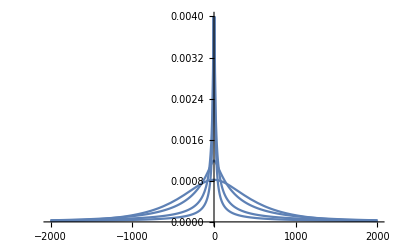

```mathematica
Plot[Table[NIntegrate[pdf1 pdf2/.{t->1,fs->10^6,g0->0,μ->10,σ->v},{x,0,∞}], {v,{1, 2, 5, 10}}],{g,-2*10^3,2*10^3},PlotRange->{0,0.004}]
```

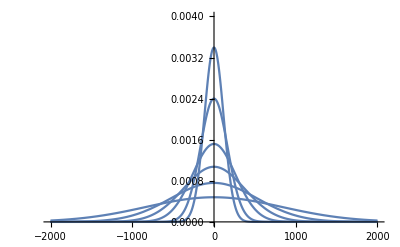

```mathematica
Plot[Table[pdf1/.{t->1,fs->10^6,g0->0,μ->10,x->1000v}, {v,{1, 2, 5, 10, 20, 50}}],{g,-2*10^3,2*10^3},PlotRange->{0,0.004}]
```

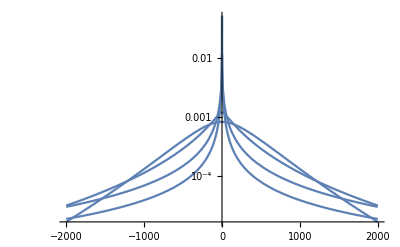

```mathematica
LogPlot[Table[NIntegrate[pdf1 pdf2/.{t->1,fs->10^6,g0->0,μ->10,σ->v},{x,0,∞}], {v,{1, 2, 5, 10}}],{g,-2*10^3,2*10^3}]
```

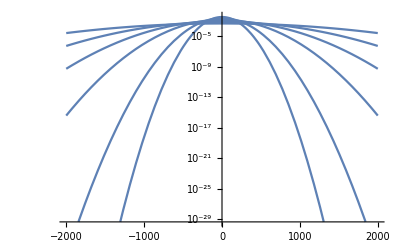

```mathematica
LogPlot[Table[pdf1/.{t->1,fs->10^6,g0->0,μ->10,x->1000v}, {v,{1, 2, 5, 10, 20, 50}}],{g,-2*10^3,2*10^3},PlotRange->{0,0.004}]
```

```mathematica
(∫_0)^∞(ⅇ^(-(g-g0)^2/(2 x Log[fs t])-(μ-Log[x])^2/(2 σ^2)))/(2 π x σ √(x Log[fs t]))dx
```

```mathematica
subs={fs->10^6,g0->25/2*10^-6,μ->-63/2,σ->2}
pdf1=PDF[NormalDistribution[g0,√(x Log[fs t])]][g]
pdf2=PDF[LogNormalDistribution[μ,σ]][x]
Plot[Table[NIntegrate[pdf1 pdf2/.subs,{x,0,∞}], {t,{1, 100, 10000, 1000000}}],{g,0,40*10^-6},PlotRange->All]
```

{fs→1000000,g0→1/80000,μ→-63/2,σ→2}

(ⅇ^(-(g-g0)^2/(2 x Log[fs t])))/(√(2 π) √(x Log[fs t]))

Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {8.97269×10^-11}. NIntegrate obtained 156.153 and 1.00497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.24323×10^-12}. NIntegrate obtained 225.906 and 1.51421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.24323×10^-12}. NIntegrate obtained 297.204 and 1.00677 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

```mathematica
pdf1=CDF[NormalDistribution[g0,√(x Log[fs t])]][g]
pdf2=PDF[LogNormalDistribution[μ,σ]][x]
FullSimplify [pdf1 pdf2,x>0]
fpdf=FullSimplify [pdf1 pdf2,x>0]/.{t->1,fs->10^6,g0->0,μ->10,σ->2}
```

1/2 Erfc[(-g+g0)/(√2 √(x Log[fs t]))]

Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

(ⅇ^(-(μ-Log[x])^2/(2 σ^2)) Erfc[(-g+g0)/(√2 √(x Log[fs t]))])/(2 √(2 π) x σ)

(ⅇ^(-1/8 (10-Log[x])^2) Erfc[-g/(√x √(2 Log[1000000]))])/(4 √(2 π) x)

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

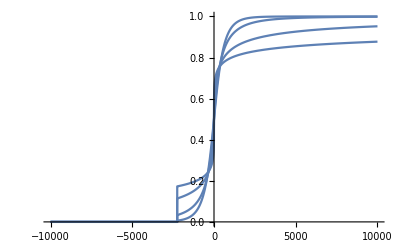

```mathematica
Plot[Table[NIntegrate[pdf1 pdf2/.{t->1,fs->10^6,g0->0,μ->10,σ->v},{x,0,∞}], {v,{1, 2, 5, 10}}],{g,-10*10^3,10*10^3},PlotRange->All]
```

{fs→1000000,g0→25/2,μ→-3.5,σ→2}

(ⅇ^(-(g-g0)^2/(2 x Log[fs t])))/(√(2 π) √(x Log[fs t]))

Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

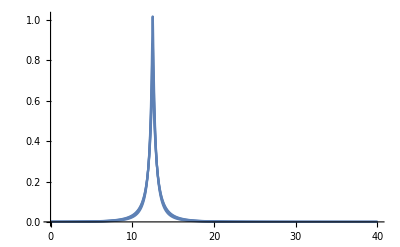

```mathematica
subs={fs->10^6,g0->25/2,μ->-3.5,σ->2}
pdf1=PDF[NormalDistribution[g0,√(x Log[fs t])]][g]
pdf2=PDF[LogNormalDistribution[μ,σ]][x]
Plot[Table[NIntegrate[pdf1 pdf2/.subs,{x,0,∞}], {t,{1, 100, 10000, 1000000}}],{g,0,40},PlotRange->All]
```

{fs→1000000,g0→25/2,μ→-3.5,σ→2}

1/2 Erfc[(-g+g0)/(√2 √(x Log[fs t]))]

Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

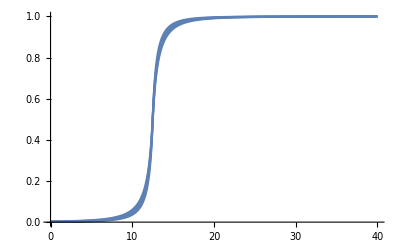

```mathematica
subs={fs->10^6,g0->25/2,μ->-3.5,σ->2}
pdf1=CDF[NormalDistribution[g0,√(x Log[fs t])]][g]
pdf2=PDF[LogNormalDistribution[μ,σ]][x]
Plot[Table[NIntegrate[pdf1 pdf2/.subs,{x,0,∞}], {t,{1, 100, 10000, 1000000}}],{g,0,40},PlotRange->All]
```

```mathematica
Table[NIntegrate[pdf1 pdf2/.subs/.{g->20},{x,0,∞}], {t,{1, 100, 10000, 1000000}}]
```

{0.995814,0.994166,0.992532,0.990925}

{fs→1000000,g0→25/2,μ→-3.5,σ→2}

ConditionalExpression[g0-√2 InverseErfc[2 p] √(x Log[fs t]), 0≤p≤1]

Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

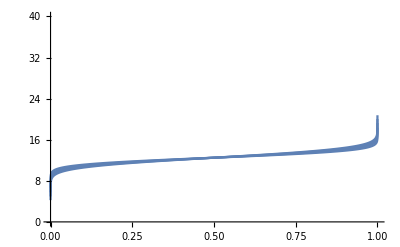

```mathematica
subs={fs->10^6,g0->25/2,μ->-3.5,σ->2}
pdf1=InverseCDF[NormalDistribution[g0,√(x Log[fs t])],p]
pdf2=PDF[LogNormalDistribution[μ,σ]][x]
Plot[Table[NIntegrate[pdf1 pdf2/.subs,{x,0,∞}], {t,{1, 100, 10000, 1000000}}],{p,0,1},PlotRange->{0,40}]
```

```mathematica
pdf1 pdf2[[1]][[1]][[1]]
```

ConditionalExpression[(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)) (g0-√2 InverseErfc[2 p] √(x Log[fs t])))/(√(2 π) x σ), 0≤p≤1]